```mathematica
Exit[]
```

Alternative utility-function

```mathematica
k=.;γ=.01;μ=0;S0=55;σ=.25;
f[k_,x_]:=x-Sqrt[k+x^2]
put[W_]:=Max[0,50-W]
xx[B_,t_]:=S0 Exp[ σ Sqrt[t] B+(μ-σ^2/2)t];
g[a_,t_]:=NIntegrate[f[-put[xx[B,t]]+a(xx[B,t]-S0)]pr[B],{B,-∞,∞}]
```

```mathematica
Plot[{g[a,1],g[a,0.5]},{a,-.5,.1}]
```

$Aborted

```mathematica
y=.;k=.;Simplify[Expand[(f[k,y+x]-f[k,y])^2]]
```

2 (k+x^2+x y+y^2+x √(k+y^2)-x √(k+(x+y)^2)-√(k+y^2) √(k+(x+y)^2))

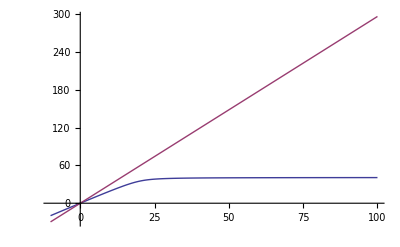

```mathematica
k=34;y=-20;Plot[{f[k,y+x]-f[k,y],(2+Abs[y/√(k+y^2)])x},{x,-10,100}]
```

```mathematica
y=.;k=.;Simplify[D[f[k,w+x],x]]
```

1-(w+x)/(√(k+(w+x)^2))

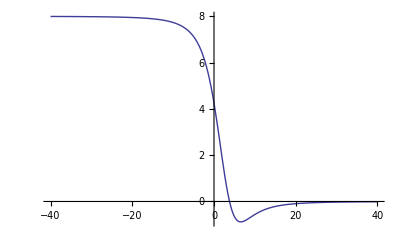

```mathematica
k=34;y=-3;Plot[-(2 (k (3 x+2 y+√(k+y^2)-2 √(k+(x+y)^2))-2 (x+y)^2 (-x-y+√(k+(x+y)^2))))/((k+(x+y)^2)^(3/2)),{x,-40,40},PlotRange->All]
```

```mathematica
Limit[1-(x+y)/(√(k+(x+y)^2)),{x->-∞}]
```

{2}

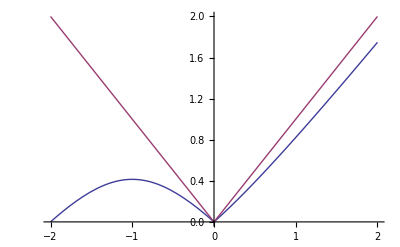

```mathematica
a=1;Plot[{(Abs[Sqrt[1+(1+x)^2]-Sqrt[2]]),Abs[x]},{x,-2,2}]
```

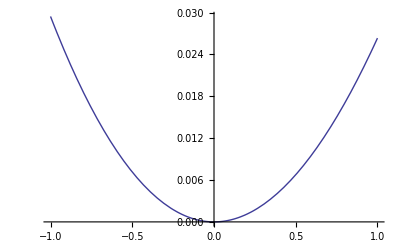

```mathematica
Plot[{f[x,3]^2},{x,-1,1}]
```

```mathematica
Limit[f[x],{x-> ∞}]
```

{1}

```mathematica
k=.
```

```mathematica
Simplify[D[f[k,x],{x,1}]]
```

1-x/(√(k+x^2))

```mathematica
Limit[1-x/(√(k+x^2)),{x-> -∞}]
```

{2}

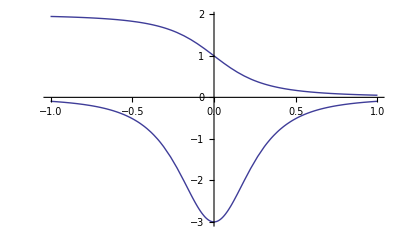

```mathematica
Plot[{1-(k x)/(√(1+k^2 x^2)),-k/((1+k^2 x^2)^(3/2))}/.k-> 3,{x,-1,1}]
```

```mathematica
Simplify[D[f[k,x],{x,2}]]
```

```mathematica
-Simplify[D[f[k,x],{x,2}]/D[f[k,x],x]]
```

(k (k x+√(1+k^2 x^2)))/(1+k^2 x^2)

```mathematica
g[k_,x_]:=(k (k x+√(1+k^2 x^2)))/(1+k^2 x^2)
```

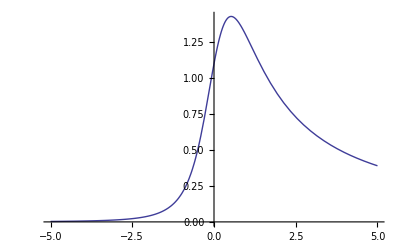

```mathematica
Plot[g[1.1,x],{x,-5,5}]
```

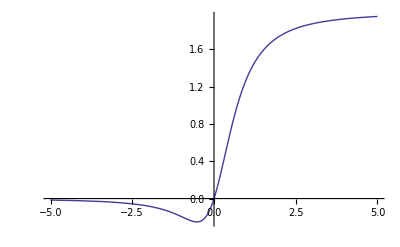

```mathematica
Plot[x g[1.1,x],{x,-5,5}]
```

```mathematica
lässt sich approximiern
```